## Syntax and Programming

Please click on the » to open collapsed sections.

## Learning Objectives

This section will introduce you to the different aspects of writing Wolfram Language code.

### Built-in Functions

Accomplish tasks using built-in functions

### Symbolic Expressions

Understand that everything in Wolfram Language is an expression

Building blocks of an expression

Anatomy of an expression

### Assignments

Assign values to symbols using the two different forms of assignment

Immediate assignment

Delayed assignment

### Function Definitions

Define your own custom functions

Use pure functions

### Lists and Doing Things Repeatedly

Making lists of expressions

Different approaches to doing things repeatedly

## Built-in Functions

There are more than 6000 functions built into Wolfram Language. These are easily identifiable:

Their names start with capital letters and they accept inputs within square brackets.

The function names are usually intuitive complete English words or standard mathematical abbreviations, making it easy to search for them in the Documentation Center.

Here are a few examples of built-in functions in action:

```mathematica
Range[10]
```

```mathematica
RandomInteger[100]
```

```mathematica
RandomInteger[100,10]
```

```mathematica
Max[44,22,7,88,94,51,12,42,34,6]
```

```mathematica
Solve[2x-7==0,x]
```

```mathematica
Integrate[Sin[x],x]
```

```mathematica
Plot[Sin[x]/x,{x,-Pi,Pi}]
```

```mathematica
ImageIdentify[-Graphics-]
```

```mathematica
WordTranslation["pancake","Dutch"]
```

You can accomplish most of your programming tasks by making use of these built-in functions.

## Symbolic Expressions

Everything in Wolfram Language is a symbolic expression: numbers, strings, built-in functions, code that you write, even the notebook in which you write the code.

The fundamental structure of a symbolic expression is as follows:

Head[elem_1, elem_2, elem_3, …]

The notion of expressions is a crucial unifying principle in the Wolfram System. It is the fact that every object in the Wolfram System has the same underlying structure that makes it possible for the Wolfram System to cover so many areas with a comparatively small number of basic operations.

Here is a simple expression:

f[x,y, …]

The meaning of f can be interpreted as:

a function with x and y as arguments or parameters: Sin[x]

a command with x and y as arguments or parameters: Print["hello world"]

an operator with x and y as operands: x+y or Plus[x,y]

a type of object with x and y as its contents: RGBColor[1,0,0]

a head with x and y as elements: {x,y,z} or List[x,y,z]

Wolfram Language does not have types as such. The “head” of an expression can be used as a kind of generalized type designator. Its purpose is to serve as a “tag” to specify the “type” of the structure.

### Some expressions look a little different

Sometimes you will run into expressions that look nothing like the template shown:

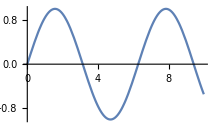

```mathematica
Entity["Country","Finland"]
```

```mathematica
{1,2,3}
```

```mathematica
a+b
```

However, you can reveal their true underlying structure with the FullForm function:

```mathematica
FullForm[a+b]
```

```mathematica
FullForm[{1,2,3} ]
```

```mathematica
FullForm[Entity["Country","Finland"]]
```


```mathematica
FullForm[-Graphics-]
```

### Special ways to input expressions

Sometimes expressions are written using postfix and prefix notations.

Standard notation:

```mathematica
f[x]
```

Prefix notation:

```mathematica
f@x
```

Postfix notation:

```mathematica
x//f
```

## Atomic Expressions

Wolfram Language symbolic expressions can represent an immense range of types of objects. All expressions are ultimately built from a small number of distinct types of atomic elements.

### Atoms

Numbers: Integer, Rational, Real, Complex and other representation of numbers:

```mathematica
127
```

```mathematica
3/4
```

```mathematica
0.0004
```

```mathematica
5+3I
```

Strings: A String is anything enclosed in double quotes:

```mathematica
"String"
```

```mathematica
"123"
```

Symbols: Basic named objects in Wolfram Language

Every symbol has a unique name. The name:

```mathematica
variable
```

```mathematica
temp
```

consists of a concatenation of letters, numbers and other characters

cannot begin with a number

cannot begin with or contain certain reserved special characters (e.g. !, @, #, %, ^, +, -, _, =, &, (, ), {, }, [, ], etc.)

Wolfram Language is fully symbolic, so “undefined variables” can always just stand for themselves:

```mathematica
x
```

```mathematica
x+x+x
```

```mathematica
Mean[{2x,7x,3x}]
```

Atomic expressions can be combined to build up composite expressions. You can also nest composite expressions to build progressively more complicated expressions:

```mathematica
x^2+2 Sin[4t+5]
```

```mathematica
Graphics[Table[{Hue[t/20],Circle[{Cos[2Pi t/20],Sin[2Pi t/20]}]},{t,20}]]
```

## Anatomy of an Expression

All expressions—whatever they may represent—ultimately have a uniform tree-like structure. Some built-in functions can be used as tools to inspect and understand composite expressions.

### FullForm of an Expression

You have already seen the FullForm function in use:

```mathematica
FullForm[x^3+(1+x)^2]
```

Plus[Power[x,3],Power[Plus[1,x],2]]

### Expressions as Trees

You can think of any Wolfram Language expression as a tree.

TreeForm prints out expressions to show their “tree” structure:

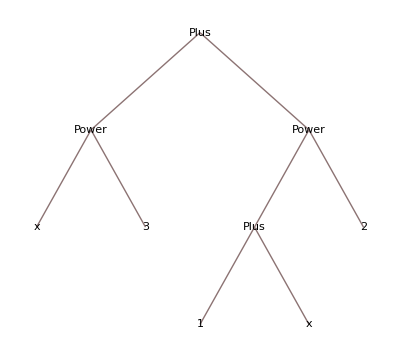

```mathematica
TreeForm[x^3+(1+x)^2]
```

### Head of an Expression

The part of the expression preceding the opening square bracket is known as the head of an expression.

Use Head to extract the head of an expression:

```mathematica
a+b/2 c
```

a+(b c)/2

```mathematica
Head[a+b/2 c]
```

Plus

### Length of an Expression

Use Length to find the number of elements in an expression:

```mathematica
Length[a+b/2 c]
```

2

```mathematica
Length[x^3+(1+x)^2 +x+6]
```

4

### Part of an Expression

Now that you have visualized expressions built out of many parts, you can think of working with these parts individually or in combination.

You can use Part to extract any part of an expression:

```mathematica
Part[(x+y+z),2]
```

y

```mathematica
(x+y+z)[[2]]
```

y

```mathematica
(x^3+(1+x)^2)[[2,1]]
```

1+x

```mathematica
{a,b,c}[[3]]
```

c

## Assignments

Values can be assigned to symbols using Set and SetDelayed. Assignments establish rules to replace the left-hand side (LHS) of an assignment with the right-hand side (RHS).

### Immediate Assignment

These are rules of the form:

LHS = RHS

The RHS is evaluated and the result is assigned to be the value of the LHS right away:

```mathematica
a=3
```

3

```mathematica
b=a^2
```

9

```mathematica
c=a+b
```

12

```mathematica
exp =c^3+(1+c)^2
```

1897

```mathematica
myList = {a,b,exp}
```

{3,9,1897}

### Delayed Assignment

An alternative is delayed assignment, where the value is recomputed every time it is needed.

Delayed assignment is specified with rules of the form:

LHS := RHS

The RHS is maintained in an unevaluated form. Whenever LHS appears in an expression, it is replaced by RHS, evaluated anew each time:

```mathematica
c:= a^2
```

```mathematica
c
```

9

```mathematica
a=2;
```

```mathematica
b
```

9

```mathematica
c
```

4

```mathematica
?b
```

```mathematica
?c
```

### Clear Assignments

Clear the assignments:

```mathematica
x=.
```

```mathematica
Clear[x,t]
```

## Defining Functions

In Wolfram Language, function definitions are just assignments that give transformation rules for patterns.

Define a function of two arguments named x and y:

```mathematica
f[x_,y_]:=x+y
```

Use the definition (function arguments go within square brackets):

```mathematica
f[4,"temp"]
```

4+temp

Clear the definition:

```mathematica
Clear[f]
```

The names like f that you use for functions in Wolfram Language are just symbols. It is recommended that you avoid using names that begin with capital letters, to prevent confusion with built-in Wolfram Language functions.

Functions can be defined by specifying their values in a sequence of cases:

```mathematica
f[0]=1
```

1

```mathematica
f[1]=1
```

1

Any undefined case is left untransformed:

```mathematica
{f[1],f[1],f[2],f[3],f[4]}
```

{1,1,f[2],f[3],f[4]}

You can add a generic definition for other inputs:

```mathematica
f[x_]:= f[x-1]+f[x-2]
```

The _ (referred to as “blank”) on the left-hand side is very important; it presents a pattern and is discussed in detail here. For now, just remember to put a _ on the left-hand side, but not on the right-hand side, of your definition. You can impose restrictions on the patterns to create different definitions for the same function so that it behaves differently for different types of inputs.

Give different definitions for what f should do when applied to a “u object” or a “v object”:

```mathematica
f[x_Integer]:=f[x-1]+f[x-2]
```

```mathematica
f[x_String]:="This function cannot work with a string input"
```

```mathematica
f[x_]:="This function only accepts integer inputs"
```

## Pure Functions

Wolfram Language allows the use of pure functions, which make it possible to have functions that can be applied to arguments without having to define explicit names for the functions.

You will usually find a pure function defined with & at the end. The argument to the function is indicated by #:

```mathematica
#^2+ 3# -2&
```

It can be applied to an input directly:

```mathematica
#^2+ 3# -2&[42]
```

1888

Pure functions can take more than one argument (multiple arguments can be indicated using #1, #2 and so on):

```mathematica
#1+2 #2+#3^3 &[a,b,c]
```

84

## Lists

Lists are a basic way to collect things together in Wolfram Language.

Examples of lists:

```mathematica
{1,2,3,4,5}
```

```mathematica
{a,42,3.14,RGBColor[1, 0, 0],"hello", x^2+3 y^3,-Graphics3D-}
```

A List can be used as:

a container of items

a set

a vector or matrix

A list of variables/expressions:

```mathematica
{a,b,c,d,e}
```

A nested list representing a matrix of integers:

```mathematica
{{1,2},{3,4}}
```

```mathematica
MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

You can use some built-in functions to easily create lists.

Generate a list of numbers up to a maximum value with Range:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1.5,12.5,0.5]
```

{1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5}

Use Table to generate a table of values:

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

```mathematica
Table[i^2,{i,5}]
```

{1,4,9,16,25}

```mathematica
Table[i^2,{i,5,50,2.5}]
```

{25.,56.25,100.,156.25,225.,306.25,400.,506.25,625.,756.25,900.,1056.25,1225.,1406.25,1600.,1806.25,2025.,2256.25,2500.}

```mathematica
Table[i^2 + j^3,{i,{a,b,c}},{j,{x,y,z}}]
```

{{4+x^3,4+y^3,4+z^3},{81+x^3,81+y^3,81+z^3},{16+x^3,16+y^3,16+z^3}}

Use the Length function to find the number of elements in a list:

```mathematica
Length[%]
```

3

% is an easy way to refer to the last output:

```mathematica
words = RandomWord[10]
```

{enviable,thrifty,apply,matriculation,snugly,wellness,stress,witless,juncture,ammunition}

The Part function can be used to refer to an element of a list by giving its “index”:

```mathematica
Part[words,2]
```

thrifty

The shortcut notation [[ ]] is used more often:

```mathematica
words[[2]]
```

thrifty

```mathematica
words[[-1]]
```

ammunition

```mathematica
words[[3;;5]]
```

{apply,matriculation,snugly}

```mathematica
words[[;;4]]
```

{enviable,thrifty,apply,matriculation}

```mathematica
words[[{1,4,8}]]
```

{enviable,matriculation,witless}

## Doing Things Repeatedly

Wolfram Language offers a number of different options when it comes to performing any computation repeatedly.

Table can be used to repeatedly apply functions to iterators:

```mathematica
Table[Total[IntegerDigits[i^2]],{i,10}]
```

{1,4,9,7,7,9,13,10,9,1}

```mathematica
Table[Framed[c,Background-> RandomColor[]],{c,Alphabet[]}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Map can also be used to perform the same operation on every element in a list:

```mathematica
Map[Framed,Alphabet[]]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Framed/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Pure functions in conjunction with Map are a powerful tool for repeated operations on elements of a list:

```mathematica
Framed[#,Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

In Wolfram Language, many functions are also automatically “listable”, so that they are always applied to every element in a list:

```mathematica
Log[E]
```

1

```mathematica
Log[{a,b,c}]
```

{Log[2],Log[9],Log[4]}

The more traditional Looping Constructs of For, While and Do are also available in Wolfram Language.

## References

Expressions

Lists

Associations

Computation with Structured Datasets

Defining Variables and Functions

Functions and Programs

Functional Operations

## Initialization

```mathematica
Clear["Global`*"]
```